```mathematica
Nxs = Table[i*32,{i,1,16}];
```

```mathematica
Nt = 640;(*151*)
ti = 0; tf =5; 
deltat = (tf - ti) /Nt ;
xi = -40; xf = 40;
(*deltax = (xf - xi) / Nx;*)
c = 1;
maxErrLD2 = Table[0,{i,1,Length[Nxs]}];
maxErrPI = Table[0,{i,1,Length[Nxs]}];
maxEnergyLD2 = Table[0,{i,1,Length[Nxs]}];
maxEnergyPI = Table[0,{i,1,Length[Nxs]}];
maxProbLD2 = Table[0,{i,1,Length[Nxs]}];
maxProbPI = Table[0,{i,1,Length[Nxs]}];
f[x_] = ⅇ^(- x^2+ⅈ x);
T = N[Table[tn = ti + n *deltat, {n, 0, Nt -1 }],32];

Subscript[δ, i_,j_]:=KroneckerDelta[i,j];
```

```mathematica
Do[
deltax = (xf - xi) / Nxs[[p]];

(************************************************************************************************************************)
(*Set Up*)
(************************************************************************************************************************)

Xp= N[Table[xm = xi + m *deltax, {m, 0, Nxs[[p]]}],32];

Xo = N[Table[xn = xi + n *deltax, {n, 0, Nxs[[p]] -1}],32];

L2 = N[Table[(NDSolve`FiniteDifferenceDerivative[Derivative[i],Xp, "DifferenceOrder"->2, PeriodicInterpolation->True]@"DifferentiationMatrix"//Normal), {i,1,8}],32];
DL2 = L2[[2]] * deltat * (ⅈ / 2);

(*LD2*)
ULD2= N[Table[0, {n, 1, Nt}, {m, 1, Nxs[[p]] }],32];
ULD2[[1,All]] = N[f[Xo],32];
ULD2 = Chop[ULD2, 10^(-307)];
ULD2 = Developer`ToPackedArray[ULD2, Complex]; 
Developer`PackedArrayQ[ULD2];

ILD2 = N[IdentityMatrix[Length[DL2]],32];
ALD2 = N[ILD2 - (DL2 / 2),32];
BLD2 = N[ILD2 + (DL2 / 2),32];
MLD2 = N[Inverse[ALD2].BLD2,32];
EMLD2 = N[MLD2 - ILD2,32];
EMLD2 = Developer`ToPackedArray[EMLD2, Real]; 

Do[ULD2[[n+1,All]] = ULD2[[n,All]] + (EMLD2).ULD2[[n,All]], {n,1,Nt - 1 }];


(*Partial Inversion*)
UP= N[Table[0, {n, 1, Nt}, {m, 1, Nxs[[p]] }],32];
UP[[1,All]] = N[f[Xo],32];
UP = Chop[UP, 10^(-307)];
UP = Developer`ToPackedArray[UP, Complex]; 
Developer`PackedArrayQ[UP];


selectwidth = 8;
diffOrder = 2;

deriv = 2;

(*The total number of points in the stencil*)
totalpoints = (2*selectwidth) + 1;

(*The middle point in the stencil*)
middlepoint = selectwidth + 1;

(*Set up the grid for the stencil*)
grid=x0+(Range[totalpoints]-middlepoint)Δx;

(LP=NDSolve`FiniteDifferenceDerivative[Derivative[deriv],grid,"DifferenceOrder"->diffOrder]@"DifferentiationMatrix"//Normal);

(*define r:=Δt/(Δx^deriv)*)
(*This is done so the M Matrix can be created symbollically and be created for any CFL Number by putting in a value for r*)
r=.;
LPX = LP*((-1)^deriv)*(r*(Δx)^deriv);

(*Manualy set up periodic boundary conditions because PeriodicInterpolation will remove removes a grid point on the end*)
(*Can use PeriodicInterpolation on the L Matrix if you add a +1 when defining the grid*)
gn = (LPX[[middlepoint,All]]//Normal)//Simplify//FullSimplify;
LPX = Table[RotateRight[gn,i],{i,-selectwidth,selectwidth}];
LPX[[1,-1]]=0;
LPX[[1,-2]]=0;
LPX[[2,-1]]=0;
LPX[[-1,1]]=0;
LPX[[-1,2]]=0;
LPX[[-2,1]]=0;
LPX[[-3,1]] = 0;
LPX[[-2,2]] = 0;
LPX[[-1,3]] = 0;
LPX[[1,-3]] = 0;
LPX[[2,-2]] = 0;
LPX[[3,-1]] = 0;
LPX = LPX//.{r -> (deltat / (deltax)^deriv)};

(*Set up Identity Matrix*)
IP=IdentityMatrix[Length[LPX]];

(*Generate a Crank–Nicolson M Matrix for the stencil*)
(Mn=Inverse[IP-(ⅈ * LPX)/4 ].(IP+(ⅈ * LPX)/4));

(*Take the middle row from this Crank-Nicolson M Matrix*)
fn=(Mn[[middlepoint,All]]//Normal)//Simplify//FullSimplify;


(*Generate a M Matrix from the L matrix for the stencil*)
MP = Table[0,{i,1,Nxs[[p]]},{j,1,Nxs[[p]]}];

(*WITHOUT Periodic Boundary Conditions Placed*)
MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]],{i,1,Nxs[[p]]},{j,1,Nxs[[p]]}];

(*WITH Periodic Boundary Conditions*)
(*MP = Table[Sum[(Subscript[δ, i,j+(middlepoint-k)])fn[[k]] + (Subscript[δ, i,(j-k)])fn[[middlepoint + k]],{k,selectwidth}] + Subscript[δ, i,j] fn[[middlepoint]] + Sum[(Subscript[δ, (i + Nx) - n,j])fn[[selectwidth - (n - 1)]] + (Subscript[δ, (i + Nx) + n,(j + 2*Nx)])fn[[(middlepoint + 1) + (n - 1)]]  ,{n,1,selectwidth}],{i,1,Nxs[[p]]},{j,1,Nxs[[p]]}];*)

Ip = IdentityMatrix[Length[MP]];

EMP = MP - Ip;

EMP= Developer`ToPackedArray[EMP, Real]; 

Do[UP[[n+1,All]] = UP[[n,All]] + (EMP).UP[[n,All]], {n,1,Nt - 1 }];


(************************************************************************************************************************)
(*Energy and Prob*)
(************************************************************************************************************************)



(*LD2*)
FLD2 = Table[0,{i,1,Nt},{j,1,Nxs[[p]]}];
FLD2 = Developer`ToPackedArray[FLD2, Real];
intLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
intLD2 = Developer`ToPackedArray[intLD2, Real];
GLD2 = Table[0,{i,1,Nt},{j,1,Nxs[[p]]}];
GLD2 = Developer`ToPackedArray[GLD2, Real];
GintLD2 = Table[0,{i,1,Length[FLD2[[All,1]]]}];
GintLD2 = Developer`ToPackedArray[GintLD2, Real];
Do[
FLD2[[i]] = Conjugate[ULD2[[i,All]]](ULD2[[i,All]])//Re;

intLD2[[i]] = (2π)/Nxs[[p]] Total[FLD2[[i,All]]];
GLD2[[i]] = -0.5Conjugate[ULD2[[i,All]]](L2[[2]].ULD2[[i,All]])//Re;

GintLD2[[i]] = (2π)/Nxs[[p]] Total[GLD2[[i,All]]]
,{i,1,Length[FLD2[[All,1]]]}];

(*Partial Inversion*)
FP= Table[0,{i,1,Nt},{j,1,Nxs[[p]]}];
FP = Developer`ToPackedArray[FP, Real];
intP = Table[0,{i,1,Length[FP[[All,1]]]}];
intP = Developer`ToPackedArray[intP, Real];
GP= Table[0,{i,1,Nt},{j,1,Nxs[[p]]}];
GP = Developer`ToPackedArray[GP, Real];
GintP = Table[0,{i,1,Length[FP[[All,1]]]}];
GintP = Developer`ToPackedArray[GintP, Real];
Do[
FP[[i]] = Conjugate[UP[[i,All]]](UP[[i,All]])//Re;

intP[[i]] = (2π)/Nxs[[p]] Total[FP[[i,All]]];
GP[[i,All]] =-0.5 Conjugate[UP[[i,All]]](L2[[2]].UP[[i,All]])//Re;

GintP[[i]] = (2π)/Nxs[[p]] Total[GP[[i,All]]]
,{i,1,Length[FP[[All,1]]]}];

probErrorLD2=Abs[GintLD2-GintLD2[[1]]];
probErrorP = Abs[GintP - GintP[[1]]];

energyErrorLD2 = Abs[intLD2 - intLD2[[1]]];
energyErrorP = Abs[intP - intP[[1]]];


maxProbLD2[[p]] = Max[probErrorLD2];
maxProbPI[[p]] = Max[probErrorP];

maxEnergyLD2[[p]] = Max[energyErrorLD2];
maxEnergyPI[[p]] = Max[energyErrorP];


(************************************************************************************************************************)
(*L1 Error*)
(************************************************************************************************************************)

fexact[t_,x_] = 1/(√(1+2 ⅈ t))Exp[(-(x-ⅈ/2)^2)/(1+2ⅈ t)-1/4];
Uexact = Table[fexact[T[[i]],Xo[[j]]],{i,1,Nt},{j,1,Nxs[[p]]}];
Uexact = Chop[N[Uexact], 10^(-307)];
Uexact = Developer`ToPackedArray[Uexact, Complex];

exacti={Re[fexact[0,Xo]],Im[fexact[0,Xo]]}//Transpose;

exactf={Re[fexact[T[[-1]],Xo]],Im[fexact[T[[-1]],Xo]]}//Transpose;



(*LD2*)
abserrLD2 = Abs[ULD2-Uexact];
errorLD2 = Table[0,{i,1,Length[abserrLD2]}];
errorLD2 = Developer`ToPackedArray[errorLD2, Real];
Do[
errorLD2[[i]] = Norm[abserrLD2[[i,All]], 1] * deltax;
,{i,1,Length[errorLD2]}
];


(*Partial Inversion*)
abserrP = Abs[UP-Uexact];
errorP = Table[0,{i,1,Length[abserrP]}];
errorP = Developer`ToPackedArray[errorP, Real];
Do[
errorP[[i]] = Norm[abserrP[[i,All]], 1] * deltax;
,{i,1,Length[errorP]}
];

maxErrLD2[[p]] = Max[errorLD2];

maxErrPI[[p]] = Max[errorP];


Print["Finished " <> ToString[Nxs[[p]]]];


,{p,1,Length[Nxs]}]
```

Finished 32

Finished 64

Finished 96

Finished 128

Finished 160

Finished 192

Finished 224

Finished 256

Finished 288

Finished 320

Finished 352

Finished 384

Finished 416

Finished 448

Finished 480

Finished 512

```mathematica
(*ListLogPlot[{probErrorLD2,probErrorP, probErrorRK2},PlotStyle->{Blue, Red, Green},PlotLegends->{"LD2","PI", "RK2"}]*)
```

```mathematica
(*ListLogPlot[{Transpose[{T,energyErrorLD2}], Transpose[{T,energyErrorP}], Transpose[{T,energyErrorRK2}]},PlotStyle->{Blue, Red, Green},PlotLegends->{"LD2","PI", "RK2"},AxesLabel->{"T","Log(|Relative Energy Error)"},PlotLabel->"Relative Energy Error",PlotRange->{{ti,tf},All},Joined->True]*)
```

```mathematica
(*ListLogPlot[{Transpose[{T,errorLD2}],Transpose[{T,errorP}],Transpose[{T,errorRK2}]},PlotRange->{{ti,tf},All}, PlotStyle->{Blue,{Red, Dashed}, Green},PlotLegends->{"LD2","PI", "RK2"},AxesLabel->{"T","Log(L1 Error)" },PlotLabel->"L1 Error", Joined->True]*)
```

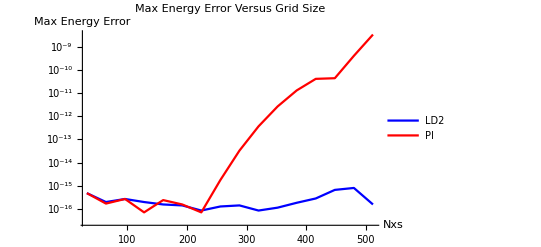

```mathematica
ListLogPlot[{Transpose[{Nxs,maxEnergyLD2}], Transpose[{Nxs,maxEnergyPI}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"Nxs","Max Energy Error"},PlotLabel->"Max Energy Error Versus Grid Size",PlotRange->{All,All},Joined->True]
```

```mathematica
maxEnergyPI[[1]]
```

4.71845×10^-16

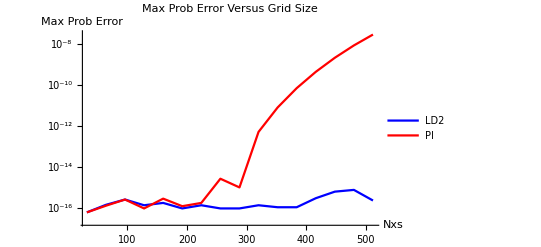

```mathematica
ListLogPlot[{Transpose[{Nxs,maxProbLD2}], Transpose[{Nxs,maxProbPI}]},PlotStyle->{Blue, Red},PlotLegends->{"LD2","PI"},AxesLabel->{"Nxs","Max Prob Error"},PlotLabel->"Max Prob Error Versus Grid Size",PlotRange->{All,All},Joined->True]
```

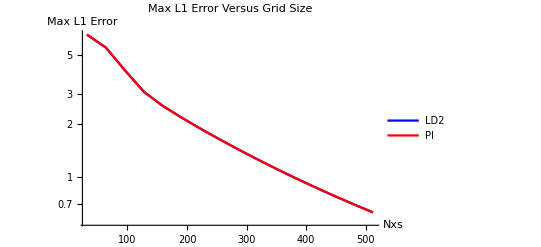

```mathematica
ListLogPlot[{Transpose[{Nxs,maxErrLD2}], Transpose[{Nxs,maxErrPI}]},PlotStyle->{Blue, {Red, Dashed}},PlotLegends->{"LD2","PI"},AxesLabel->{"Nxs","Max L1 Error"},PlotLabel->"Max L1 Error Versus Grid Size",PlotRange->{All,All},Joined->True]
```

```mathematica
maxErrLD2
```

{6.50868,5.48051,4.06316,3.06226,2.54091,2.1748,1.87911,1.63393,1.4282,1.25429,1.10652,0.980407,0.87237,0.779475,0.69931,0.629879}

```mathematica
maxErrPI
```

{6.50868,5.48051,4.06316,3.06226,2.54091,2.1748,1.87911,1.63393,1.4282,1.25429,1.10652,0.980407,0.87237,0.779475,0.69931,0.629879}

```mathematica
32*11
```

352